```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=0.1;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

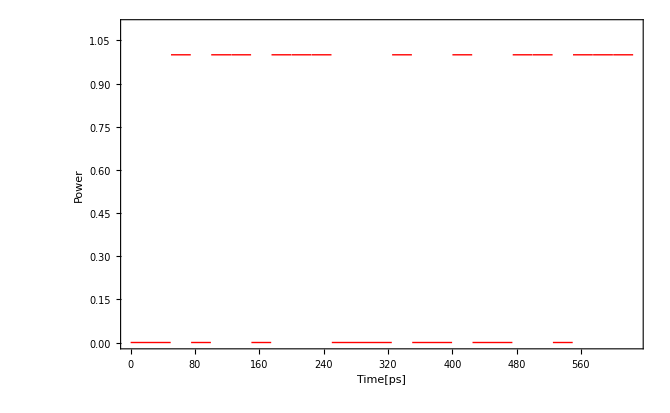

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->30},PlotRange->{0,1.1}]
```

1/2 (1+Cos[400000000000000 π t])

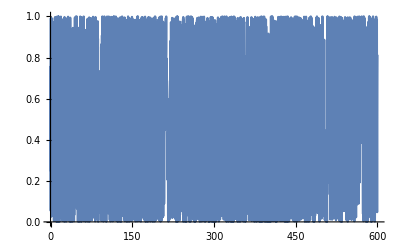

1/2 (1+Cos[400000000000000 π t]) (If[1/40000000000<t<1/20000000000,0,0]+If[1/20000000000<t<3/40000000000,1,0]+If[3/40000000000<t<1/10000000000,0,0]+If[1/10000000000<t<1/8000000000,1,0]+If[1/8000000000<t<3/20000000000,1,0]+If[3/20000000000<t<7/40000000000,0,0]+If[7/40000000000<t<1/5000000000,1,0]+If[1/5000000000<t<9/40000000000,1,0]+If[9/40000000000<t<1/4000000000,1,0]+If[1/4000000000<t<11/40000000000,0,0]+If[11/40000000000<t<3/10000000000,0,0]+If[3/10000000000<t<13/40000000000,0,0]+If[13/40000000000<t<7/20000000000,1,0]+If[7/20000000000<t<3/8000000000,0,0]+If[3/8000000000<t<1/2500000000,0,0]+If[1/2500000000<t<17/40000000000,1,0]+If[17/40000000000<t<9/20000000000,0,0]+If[9/20000000000<t<19/40000000000,0,0]+If[19/40000000000<t<1/2000000000,1,0]+If[1/2000000000<t<21/40000000000,1,0]+If[21/40000000000<t<11/20000000000,0,0]+If[11/20000000000<t<23/40000000000,1,0]+If[23/40000000000<t<3/5000000000,1,0]+If[3/5000000000<t<1/1600000000,1,0]+If[1/1600000000<t<13/20000000000,1,0])

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t]= (Cos[2*Pi*Fc*t]+1)/2
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
```

```mathematica
∫_0^(bit*25*10^-12) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-((ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))
```

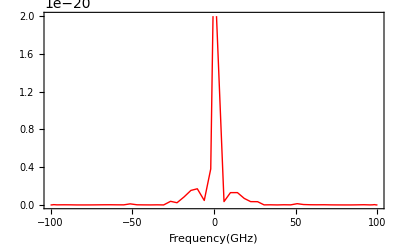

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

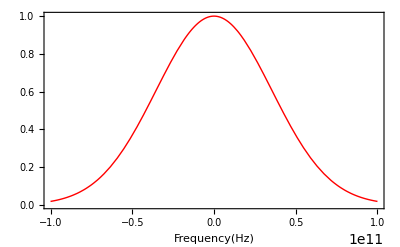

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

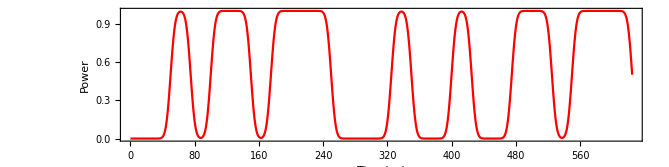

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

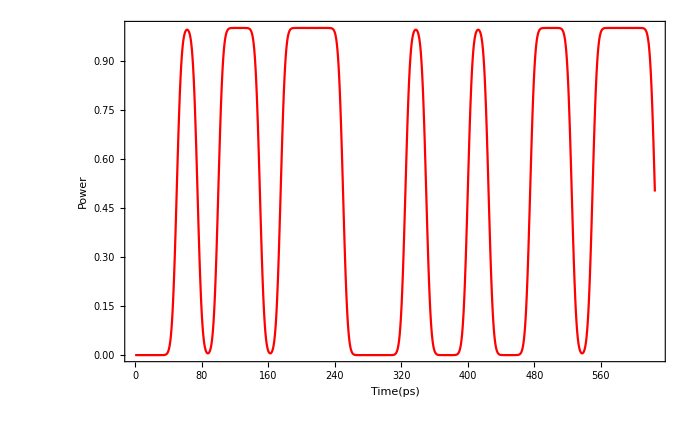

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
f[x_]:=1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)];
```

```mathematica
FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]
```

{9.87697×10^15,{x1→2.4694}}

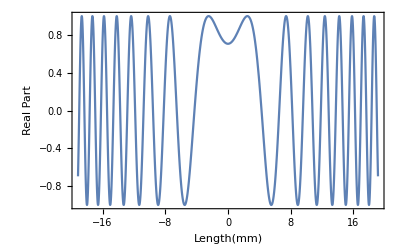

```mathematica
max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]
```

## Impulse Responce for Fiber Dispersion

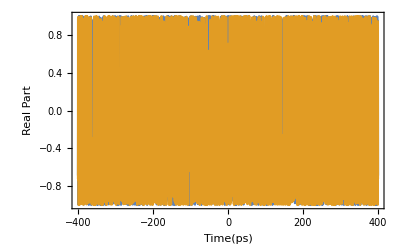

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
hcmp[t_]:=
(*1/(√(2*Pi*β2*80))*10^6*)Exp[+ⅈ*(t^2/(2*β2*100)-Pi/4)];
```

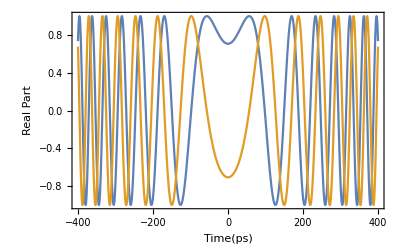

```mathematica
Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]
```

```mathematica
IntegerPart[total*10^12]
```

784

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

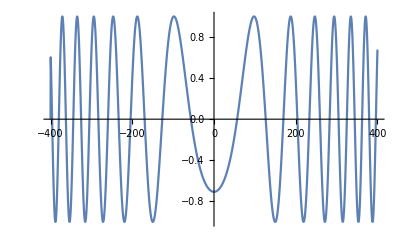

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

## Simulation

```mathematica
simu0[a_]:=simu0[a]=Sum[hdis2[z]*hcmp3[a-z],{z,-10000,10000,samp}]
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*simu0[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

1233.79-7850.33 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,7946.69},{-99.5,7929.63},{-99.,7912.48},{-98.5,7895.14},{-98.,7877.51},{-97.5,7859.47},{-97.,7840.86},{-96.5,7821.5},{-96.,7801.21},{-95.5,7779.79},{-95.,7757.02},{-94.5,7732.67},{-94.,7706.54},{-93.5,7678.37},{-93.,7647.95},{-92.5,7615.04},{-92.,7579.42},{-91.5,7540.89},{-91.,7499.23},{-90.5,7454.26},{-90.,7405.82},{-89.5,7353.75},{-89.,7297.94},{-88.5,7238.3},{-88.,7174.78},{-87.5,7107.35},{-87.,7036.06},{-86.5,6960.96},{-86.,6882.2},{-85.5,6799.94},{-85.,6714.43},{-84.5,6625.96},{-84.,6534.9},{-83.5,6441.68},{-83.,6346.78},{-82.5,6250.76},{-82.,6154.25},{-81.5,6057.93},{-81.,5962.55},{-80.5,5868.91},{-80.,5777.84},{-79.5,5690.25},{-79.,5607.02},{-78.5,5529.08},{-78.,5457.32},{-77.5,5392.61},{-77.,5335.75},{-76.5,5287.43},{-76.,5248.25},{-75.5,5218.62},{-75.,5198.8},{-74.5,5188.82},{-74.,5188.52},{-73.5,5197.49},{-73.,5215.12},{-72.5,5240.57},{-72.,5272.84},{-71.5,5310.72},{-71.,5352.93},{-70.5,5398.04},{-70.,5444.59},{-69.5,5491.08},{-69.,5536.},{-68.5,5577.9},{-68.,5615.36},{-67.5,5647.04},{-67.,5671.68},{-66.5,5688.13},{-66.,5695.36},{-65.5,5692.42},{-65.,5678.53},{-64.5,5653.},{-64.,5615.27},{-63.5,5564.9},{-63.,5501.59},{-62.5,5425.16},{-62.,5335.53},{-61.5,5232.77},{-61.,5117.05},{-60.5,4988.69},{-60.,4848.09},{-59.5,4695.81},{-59.,4532.53},{-58.5,4359.06},{-58.,4176.36},{-57.5,3985.53},{-57.,3787.87},{-56.5,3584.86},{-56.,3378.24},{-55.5,3170.01},{-55.,2962.54},{-54.5,2758.66},{-54.,2561.72},{-53.5,2375.73},{-53.,2205.46},{-52.5,2056.38},{-52.,1934.44},{-51.5,1845.47},{-51.,1794.11},{-50.5,1782.66},{-50.,1810.27},{-49.5,1873.02},{-49.,1964.9},{-48.5,2079.07},{-48.,2208.86},{-47.5,2348.32},{-47.,2492.41},{-46.5,2636.98},{-46.,2778.63},{-45.5,2914.58},{-45.,3042.59},{-44.5,3160.8},{-44.,3267.72},{-43.5,3362.14},{-43.,3443.1},{-42.5,3509.88},{-42.,3561.96},{-41.5,3598.98},{-41.,3620.8},{-40.5,3627.41},{-40.,3618.96},{-39.5,3595.78},{-39.,3558.32},{-38.5,3507.17},{-38.,3443.07},{-37.5,3366.89},{-37.,3279.65},{-36.5,3182.52},{-36.,3076.81},{-35.5,2964.02},{-35.,2845.84},{-34.5,2724.19},{-34.,2601.24},{-33.5,2479.44},{-33.,2361.58},{-32.5,2250.77},{-32.,2150.43},{-31.5,2064.23},{-31.,1995.82},{-30.5,1948.62},{-30.,1925.34},{-29.5,1927.67},{-29.,1955.97},{-28.5,2009.27},{-28.,2085.51},{-27.5,2181.93},{-27.,2295.48},{-26.5,2423.11},{-26.,2562.03},{-25.5,2709.79},{-25.,2864.33},{-24.5,3023.93},{-24.,3187.21},{-23.5,3353.08},{-23.,3520.67},{-22.5,3689.33},{-22.,3858.55},{-21.5,4027.96},{-21.,4197.3},{-20.5,4366.39},{-20.,4535.11},{-19.5,4703.37},{-19.,4871.13},{-18.5,5038.36},{-18.,5205.03},{-17.5,5371.12},{-17.,5536.58},{-16.5,5701.33},{-16.,5865.29},{-15.5,6028.31},{-15.,6190.21},{-14.5,6350.77},{-14.,6509.72},{-13.5,6666.73},{-13.,6821.41},{-12.5,6973.35},{-12.,7122.08},{-11.5,7267.08},{-11.,7407.81},{-10.5,7543.7},{-10.,7674.17},{-9.5,7798.6},{-9.,7916.42},{-8.5,8027.02},{-8.,8129.85},{-7.5,8224.36},{-7.,8310.05},{-6.5,8386.45},{-6.,8453.17},{-5.5,8509.86},{-5.,8556.22},{-4.5,8592.04},{-4.,8617.18},{-3.5,8631.56},{-3.,8635.2},{-2.5,8628.17},{-2.,8610.63},{-1.5,8582.83},{-1.,8545.06},{-0.5,8497.71},{0.,8441.23},{0.5,8376.11},{1.,8302.91},{1.5,8222.24},{2.,8134.75},{2.5,8041.11},{3.,7942.02},{3.5,7838.21},{4.,7730.38},{4.5,7619.27},{5.,7505.56},{5.5,7389.95},{6.,7273.08},{6.5,7155.57},{7.,7037.97},{7.5,6920.82},{8.,6804.55},{8.5,6689.56},{9.,6576.17},{9.5,6464.66},{10.,6355.2},{10.5,6247.93},{11.,6142.91},{11.5,6040.13},{12.,5939.55},{12.5,5841.06},{13.,5744.51},{13.5,5649.74},{14.,5556.52},{14.5,5464.62},{15.,5373.81},{15.5,5283.83},{16.,5194.41},{16.5,5105.32},{17.,5016.29},{17.5,4927.09},{18.,4837.47},{18.5,4747.23},{19.,4656.15},{19.5,4564.01},{20.,4470.61},{20.5,4375.76},{21.,4279.26},{21.5,4180.89},{22.,4080.47},{22.5,3977.77},{23.,3872.56},{23.5,3764.64},{24.,3653.75},{24.5,3539.67},{25.,3422.16},{25.5,3301.01},{26.,3175.99},{26.5,3046.94},{27.,2913.69},{27.5,2776.14},{28.,2634.26},{28.5,2488.04},{29.,2337.62},{29.5,2183.19},{30.,2025.1},{30.5,1863.85},{31.,1700.14},{31.5,1534.99},{32.,1369.82},{32.5,1206.69},{33.,1048.73},{33.5,900.84},{34.,770.89},{34.5,671.061},{35.,617.126},{35.5,621.196},{36.,681.395},{36.5,783.398},{37.,911.325},{37.5,1053.51},{38.,1202.44},{38.5,1353.3},{39.,1502.88},{39.5,1648.88},{40.,1789.59},{40.5,1923.63},{41.,2049.92},{41.5,2167.55},{42.,2275.76},{42.5,2373.96},{43.,2461.65},{43.5,2538.51},{44.,2604.3},{44.5,2658.95},{45.,2702.52},{45.5,2735.21},{46.,2757.4},{46.5,2769.62},{47.,2772.6},{47.5,2767.25},{48.,2754.7},{48.5,2736.31},{49.,2713.67},{49.5,2688.59},{50.,2663.13},{50.5,2639.56},{51.,2620.29},{51.5,2607.84},{52.,2604.69},{52.5,2613.18},{53.,2635.36},{53.5,2672.8},{54.,2726.54},{54.5,2796.97},{55.,2883.86},{55.5,2986.4},{56.,3103.29},{56.5,3232.88},{57.,3373.24},{57.5,3522.33},{58.,3678.04},{58.5,3838.28},{59.,4000.99},{59.5,4164.24},{60.,4326.17},{60.5,4485.06},{61.,4639.28},{61.5,4787.37},{62.,4927.98},{62.5,5059.87},{63.,5181.96},{63.5,5293.27},{64.,5392.95},{64.5,5480.27},{65.,5554.62},{65.5,5615.51},{66.,5662.54},{66.5,5695.45},{67.,5714.06},{67.5,5718.29},{68.,5708.17},{68.5,5683.82},{69.,5645.44},{69.5,5593.33},{70.,5527.85},{70.5,5449.46},{71.,5358.65},{71.5,5256.02},{72.,5142.2},{72.5,5017.88},{73.,4883.8},{73.5,4740.73},{74.,4589.5},{74.5,4430.93},{75.,4265.9},{75.5,4095.29},{76.,3919.99},{76.5,3740.92},{77.,3559.01},{77.5,3375.22},{78.,3190.54},{78.5,3006.02},{79.,2822.79},{79.5,2642.1},{80.,2465.39},{80.5,2294.34},{81.,2130.95},{81.5,1977.68},{82.,1837.51},{82.5,1714.06},{83.,1611.46},{83.5,1534.14},{84.,1486.23},{84.5,1470.75},{85.,1488.78},{85.5,1539.21},{86.,1619.01},{86.5,1724.08},{87.,1850.06},{87.5,1992.88},{88.,2149.05},{88.5,2315.67},{89.,2490.4},{89.5,2671.38},{90.,2857.05},{90.5,3046.17},{91.,3237.65},{91.5,3430.55},{92.,3624.05},{92.5,3817.36},{93.,4009.76},{93.5,4200.52},{94.,4388.95},{94.5,4574.34},{95.,4756.},{95.5,4933.21},{96.,5105.26},{96.5,5271.41},{97.,5430.94},{97.5,5583.13},{98.,5727.25},{98.5,5862.61},{99.,5988.51},{99.5,6104.32},{100.,6209.4},{100.5,6303.19},{101.,6385.19},{101.5,6454.94},{102.,6512.06},{102.5,6556.26},{103.,6587.31},{103.5,6605.08},{104.,6609.53},{104.5,6600.71},{105.,6578.74},{105.5,6543.87},{106.,6496.41},{106.5,6436.74},{107.,6365.34},{107.5,6282.76},{108.,6189.58},{108.5,6086.49},{109.,5974.17},{109.5,5853.39},{110.,5724.92},{110.5,5589.57},{111.,5448.17},{111.5,5301.57},{112.,5150.62},{112.5,4996.17},{113.,4839.08},{113.5,4680.22},{114.,4520.43},{114.5,4360.56},{115.,4201.46},{115.5,4043.96},{116.,3888.89},{116.5,3737.06},{117.,3589.3},{117.5,3446.4},{118.,3309.16},{118.5,3178.36},{119.,3054.78},{119.5,2939.16},{120.,2832.25},{120.5,2734.73},{121.,2647.25},{121.5,2570.39},{122.,2504.67},{122.5,2450.46},{123.,2408.06},{123.5,2377.59},{124.,2359.03},{124.5,2352.2},{125.,2356.76},{125.5,2372.25},{126.,2398.04},{126.5,2433.45},{127.,2477.69},{127.5,2529.94},{128.,2589.34},{128.5,2655.04},{129.,2726.16},{129.5,2801.88},{130.,2881.38},{130.5,2963.9},{131.,3048.68},{131.5,3135.05},{132.,3222.36},{132.5,3310.01},{133.,3397.48},{133.5,3484.27},{134.,3569.98},{134.5,3654.22},{135.,3736.71},{135.5,3817.2},{136.,3895.52},{136.5,3971.55},{137.,4045.22},{137.5,4116.53},{138.,4185.53},{138.5,4252.32},{139.,4317.02},{139.5,4379.81},{140.,4440.92},{140.5,4500.56},{141.,4559.},{141.5,4616.52},{142.,4673.39},{142.5,4729.9},{143.,4786.33},{143.5,4842.96},{144.,4900.04},{144.5,4957.84},{145.,5016.56},{145.5,5076.42},{146.,5137.59},{146.5,5200.23},{147.,5264.46},{147.5,5330.4},{148.,5398.12},{148.5,5467.68},{149.,5539.14},{149.5,5612.52},{150.,5687.84},{150.5,5765.11},{151.,5844.33},{151.5,5925.52},{152.,6008.67},{152.5,6093.78},{153.,6180.86},{153.5,6269.92},{154.,6360.97},{154.5,6454.01},{155.,6549.06},{155.5,6646.13},{156.,6745.21},{156.5,6846.3},{157.,6949.39},{157.5,7054.43},{158.,7161.39},{158.5,7270.17},{159.,7380.7},{159.5,7492.83},{160.,7606.42},{160.5,7721.27},{161.,7837.18},{161.5,7953.89},{162.,8071.12},{162.5,8188.57},{163.,8305.9},{163.5,8422.76},{164.,8538.76},{164.5,8653.52},{165.,8766.62},{165.5,8877.65},{166.,8986.19},{166.5,9091.81},{167.,9194.1},{167.5,9292.64},{168.,9387.02},{168.5,9476.86},{169.,9561.76},{169.5,9641.37},{170.,9715.34},{170.5,9783.34},{171.,9845.06},{171.5,9900.22},{172.,9948.56},{172.5,9989.83},{173.,10023.8},{173.5,10050.4},{174.,10069.4},{174.5,10080.6},{175.,10084.},{175.5,10079.5},{176.,10067.1},{176.5,10046.8},{177.,10018.6},{177.5,9982.64},{178.,9938.88},{178.5,9887.49},{179.,9828.6},{179.5,9762.35},{180.,9688.9},{180.5,9608.43},{181.,9521.12},{181.5,9427.16},{182.,9326.75},{182.5,9220.09},{183.,9107.38},{183.5,8988.84},{184.,8864.68},{184.5,8735.15},{185.,8600.47},{185.5,8460.92},{186.,8316.79},{186.5,8168.4},{187.,8016.09},{187.5,7860.27},{188.,7701.35},{188.5,7539.84},{189.,7376.26},{189.5,7211.2},{190.,7045.32},{190.5,6879.31},{191.,6713.93},{191.5,6550.02},{192.,6388.43},{192.5,6230.09},{193.,6075.97},{193.5,5927.05},{194.,5784.37},{194.5,5648.95},{195.,5521.8},{195.5,5403.91},{196.,5296.2},{196.5,5199.51},{197.,5114.54},{197.5,5041.86},{198.,4981.85},{198.5,4934.69},{199.,4900.33},{199.5,4878.5},{200.,4868.7},{200.5,4870.22},{201.,4882.14},{201.5,4903.4},{202.,4932.79},{202.5,4969.01},{203.,5010.72},{203.5,5056.54},{204.,5105.1},{204.5,5155.09},{205.,5205.22},{205.5,5254.3},{206.,5301.25},{206.5,5345.06},{207.,5384.84},{207.5,5419.83},{208.,5449.36},{208.5,5472.91},{209.,5490.06},{209.5,5500.51},{210.,5504.11},{210.5,5500.77},{211.,5490.56},{211.5,5473.64},{212.,5450.26},{212.5,5420.81},{213.,5385.72},{213.5,5345.55},{214.,5300.92},{214.5,5252.55},{215.,5201.18},{215.5,5147.65},{216.,5092.84},{216.5,5037.65},{217.,4983.01},{217.5,4929.89},{218.,4879.21},{218.5,4831.91},{219.,4788.89},{219.5,4750.97},{220.,4718.94},{220.5,4693.47},{221.,4675.15},{221.5,4664.42},{222.,4661.63},{222.5,4666.96},{223.,4680.49},{223.5,4702.12},{224.,4731.65},{224.5,4768.76},{225.,4813.01},{225.5,4863.89},{226.,4920.8},{226.5,4983.11},{227.,5050.14},{227.5,5121.21},{228.,5195.62},{228.5,5272.72},{229.,5351.86},{229.5,5432.43},{230.,5513.9},{230.5,5595.77},{231.,5677.6},{231.5,5759.05},{232.,5839.81},{232.5,5919.66},{233.,5998.45},{233.5,6076.09},{234.,6152.57},{234.5,6227.91},{235.,6302.2},{235.5,6375.59},{236.,6448.24},{236.5,6520.37},{237.,6592.2},{237.5,6663.99},{238.,6735.99},{238.5,6808.45},{239.,6881.63},{239.5,6955.75},{240.,7031.05},{240.5,7107.7},{241.,7185.86},{241.5,7265.68},{242.,7347.23},{242.5,7430.58},{243.,7515.74},{243.5,7602.68},{244.,7691.34},{244.5,7781.62},{245.,7873.39},{245.5,7966.47},{246.,8060.66},{246.5,8155.75},{247.,8251.48},{247.5,8347.61},{248.,8443.85},{248.5,8539.93},{249.,8635.58},{249.5,8730.52},{250.,8824.5},{250.5,8917.27},{251.,9008.59},{251.5,9098.28},{252.,9186.14},{252.5,9272.02},{253.,9355.8},{253.5,9437.38},{254.,9516.69},{254.5,9593.7},{255.,9668.38},{255.5,9740.73},{256.,9810.79},{256.5,9878.59},{257.,9944.18},{257.5,10007.6},{258.,10068.9},{258.5,10128.2},{259.,10185.5},{259.5,10240.9},{260.,10294.4},{260.5,10346.},{261.,10395.8},{261.5,10443.8},{262.,10490.},{262.5,10534.4},{263.,10577.},{263.5,10617.9},{264.,10657.},{264.5,10694.4},{265.,10730.1},{265.5,10764.2},{266.,10796.6},{266.5,10827.6},{267.,10857.2},{267.5,10885.4},{268.,10912.4},{268.5,10938.4},{269.,10963.4},{269.5,10987.7},{270.,11011.3},{270.5,11034.5},{271.,11057.3},{271.5,11080.},{272.,11102.8},{272.5,11125.6},{273.,11148.8},{273.5,11172.3},{274.,11196.4},{274.5,11221.1},{275.,11246.4},{275.5,11272.5},{276.,11299.4},{276.5,11327.1},{277.,11355.6},{277.5,11384.8},{278.,11414.8},{278.5,11445.4},{279.,11476.6},{279.5,11508.4},{280.,11540.5},{280.5,11572.9},{281.,11605.4},{281.5,11637.9},{282.,11670.3},{282.5,11702.2},{283.,11733.6},{283.5,11764.2},{284.,11793.9},{284.5,11822.4},{285.,11849.4},{285.5,11874.8},{286.,11898.3},{286.5,11919.6},{287.,11938.5},{287.5,11954.6},{288.,11967.7},{288.5,11977.6},{289.,11983.9},{289.5,11986.3},{290.,11984.6},{290.5,11978.5},{291.,11967.6},{291.5,11951.9},{292.,11930.9},{292.5,11904.5},{293.,11872.5},{293.5,11834.7},{294.,11790.9},{294.5,11741.},{295.,11685.},{295.5,11622.6},{296.,11554.},{296.5,11479.2},{297.,11398.2},{297.5,11311.2},{298.,11218.3},{298.5,11119.8},{299.,11015.9},{299.5,10906.9},{300.,10793.3},{300.5,10675.4},{301.,10553.8},{301.5,10428.8},{302.,10301.1},{302.5,10171.2},{303.,10039.7},{303.5,9907.15},{304.,9774.22},{304.5,9641.48},{305.,9509.5},{305.5,9378.83},{306.,9249.98},{306.5,9123.42},{307.,8999.55},{307.5,8878.71},{308.,8761.17},{308.5,8647.11},{309.,8536.64},{309.5,8429.79},{310.,8326.49},{310.5,8226.6},{311.,8129.94},{311.5,8036.24},{312.,7945.21},{312.5,7856.51},{313.,7769.8},{313.5,7684.76},{314.,7601.05},{314.5,7518.41},{315.,7436.59},{315.5,7355.42},{316.,7274.82},{316.5,7194.76},{317.,7115.32},{317.5,7036.67},{318.,6959.06},{318.5,6882.84},{319.,6808.46},{319.5,6736.43},{320.,6667.36},{320.5,6601.91},{321.,6540.8},{321.5,6484.79},{322.,6434.66},{322.5,6391.21},{323.,6355.21},{323.5,6327.42},{324.,6308.52},{324.5,6299.14},{325.,6299.81},{325.5,6310.96},{326.,6332.88},{326.5,6365.74},{327.,6409.57},{327.5,6464.25},{328.,6529.53},{328.5,6605.01},{329.,6690.17},{329.5,6784.39},{330.,6886.93},{330.5,6996.98},{331.,7113.66},{331.5,7236.03},{332.,7363.12},{332.5,7493.93},{333.,7627.48},{333.5,7762.75},{334.,7898.77},{334.5,8034.58},{335.,8169.26},{335.5,8301.92},{336.,8431.76},{336.5,8557.98},{337.,8679.9},{337.5,8796.86},{338.,8908.31},{338.5,9013.75},{339.,9112.76},{339.5,9205.03},{340.,9290.29},{340.5,9368.38},{341.,9439.22},{341.5,9502.8},{342.,9559.18},{342.5,9608.53},{343.,9651.07},{343.5,9687.07},{344.,9716.91},{344.5,9740.98},{345.,9759.75},{345.5,9773.72},{346.,9783.42},{346.5,9789.44},{347.,9792.34},{347.5,9792.73},{348.,9791.21},{348.5,9788.38},{349.,9784.83},{349.5,9781.13},{350.,9777.83},{350.5,9775.44},{351.,9774.45},{351.5,9775.3},{352.,9778.39},{352.5,9784.09},{353.,9792.71},{353.5,9804.49},{354.,9819.64},{354.5,9838.32},{355.,9860.62},{355.5,9886.6},{356.,9916.24},{356.5,9949.49},{357.,9986.24},{357.5,10026.4},{358.,10069.6},{358.5,10115.9},{359.,10164.8},{359.5,10216.1},{360.,10269.5},{360.5,10324.6},{361.,10381.2},{361.5,10438.7},{362.,10496.9},{362.5,10555.3},{363.,10613.5},{363.5,10671.1},{364.,10727.7},{364.5,10782.7},{365.,10835.7},{365.5,10886.3},{366.,10934.},{366.5,10978.3},{367.,11018.6},{367.5,11054.5},{368.,11085.5},{368.5,11111.2},{369.,11131.},{369.5,11144.5},{370.,11151.3},{370.5,11151.},{371.,11143.4},{371.5,11128.},{372.,11104.8},{372.5,11073.4},{373.,11033.9},{373.5,10986.3},{374.,10930.5},{374.5,10866.7},{375.,10795.1},{375.5,10716.},{376.,10629.8},{376.5,10536.9},{377.,10437.8},{377.5,10333.},{378.,10223.3},{378.5,10109.3},{379.,9991.7},{379.5,9871.43},{380.,9749.28},{380.5,9626.15},{381.,9502.96},{381.5,9380.65},{382.,9260.19},{382.5,9142.55},{383.,9028.72},{383.5,8919.65},{384.,8816.31},{384.5,8719.6},{385.,8630.43},{385.5,8549.62},{386.,8477.94},{386.5,8416.1},{387.,8364.71},{387.5,8324.28},{388.,8295.25},{388.5,8277.92},{389.,8272.47},{389.5,8278.98},{390.,8297.39},{390.5,8327.54},{391.,8369.14},{391.5,8421.8},{392.,8485.02},{392.5,8558.21},{393.,8640.7},{393.5,8731.76},{394.,8830.57},{394.5,8936.3},{395.,9048.05},{395.5,9164.9},{396.,9285.93},{396.5,9410.19},{397.,9536.71},{397.5,9664.56},{398.,9792.78},{398.5,9920.45},{399.,10046.7},{399.5,10170.5},{400.,10291.1},{400.5,10407.7},{401.,10519.5},{401.5,10625.6},{402.,10725.5},{402.5,10818.4},{403.,10903.7},{403.5,10981.},{404.,11049.6},{404.5,11109.2},{405.,11159.5},{405.5,11200.},{406.,11230.7},{406.5,11251.3},{407.,11261.8},{407.5,11262.2},{408.,11252.4},{408.5,11232.7},{409.,11203.3},{409.5,11164.2},{410.,11116.},{410.5,11058.9},{411.,10993.2},{411.5,10919.6},{412.,10838.4},{412.5,10750.1},{413.,10655.3},{413.5,10554.5},{414.,10448.3},{414.5,10337.1},{415.,10221.6},{415.5,10102.2},{416.,9979.48},{416.5,9853.93},{417.,9726.01},{417.5,9596.17},{418.,9464.86},{418.5,9332.48},{419.,9199.44},{419.5,9066.1},{420.,8932.86},{420.5,8800.05},{421.,8668.06},{421.5,8537.22},{422.,8407.89},{422.5,8280.45},{423.,8155.27},{423.5,8032.73},{424.,7913.23},{424.5,7797.18},{425.,7685.03},{425.5,7577.24},{426.,7474.28},{426.5,7376.68},{427.,7284.97},{427.5,7199.73},{428.,7121.55},{428.5,7051.05},{429.,6988.89},{429.5,6935.72},{430.,6892.22},{430.5,6859.05},{431.,6836.85},{431.5,6826.22},{432.,6827.7},{432.5,6841.76},{433.,6868.75},{433.5,6908.91},{434.,6962.35},{434.5,7029.},{435.,7108.66},{435.5,7200.95},{436.,7305.32},{436.5,7421.07},{437.,7547.34},{437.5,7683.15},{438.,7827.4},{438.5,7978.89},{439.,8136.32},{439.5,8298.38},{440.,8463.66},{440.5,8630.79},{441.,8798.34},{441.5,8964.94},{442.,9129.22},{442.5,9289.88},{443.,9445.66},{443.5,9595.36},{444.,9737.87},{444.5,9872.18},{445.,9997.34},{445.5,10112.5},{446.,10217.},{446.5,10310.1},{447.,10391.4},{447.5,10460.5},{448.,10517.},{448.5,10560.7},{449.,10591.6},{449.5,10609.6},{450.,10614.8},{450.5,10607.4},{451.,10587.7},{451.5,10556.},{452.,10512.7},{452.5,10458.2},{453.,10393.2},{453.5,10318.},{454.,10233.5},{454.5,10140.1},{455.,10038.8},{455.5,9930.07},{456.,9814.83},{456.5,9693.84},{457.,9567.92},{457.5,9437.9},{458.,9304.62},{458.5,9168.95},{459.,9031.74},{459.5,8893.83},{460.,8756.09},{460.5,8619.33},{461.,8484.38},{461.5,8352.01},{462.,8222.97},{462.5,8098.},{463.,7977.75},{463.5,7862.85},{464.,7753.88},{464.5,7651.34},{465.,7555.7},{465.5,7467.32},{466.,7386.51},{466.5,7313.53},{467.,7248.52},{467.5,7191.57},{468.,7142.67},{468.5,7101.74},{469.,7068.61},{469.5,7043.03},{470.,7024.67},{470.5,7013.13},{471.,7007.9},{471.5,7008.45},{472.,7014.14},{472.5,7024.28},{473.,7038.15},{473.5,7054.94},{474.,7073.84},{474.5,7093.99},{475.,7114.52},{475.5,7134.53},{476.,7153.16},{476.5,7169.51},{477.,7182.72},{477.5,7191.98},{478.,7196.48},{478.5,7195.47},{479.,7188.25},{479.5,7174.18},{480.,7152.68},{480.5,7123.25},{481.,7085.44},{481.5,7038.9},{482.,6983.34},{482.5,6918.56},{483.,6844.42},{483.5,6760.89},{484.,6667.99},{484.5,6565.83},{485.,6454.59},{485.5,6334.52},{486.,6205.93},{486.5,6069.22},{487.,5924.8},{487.5,5773.19},{488.,5614.92},{488.5,5450.59},{489.,5280.82},{489.5,5106.3},{490.,4927.71},{490.5,4745.81},{491.,4561.34},{491.5,4375.12},{492.,4187.95},{492.5,4000.68},{493.,3814.2},{493.5,3629.43},{494.,3447.33},{494.5,3268.93},{495.,3095.34},{495.5,2927.78},{496.,2767.57},{496.5,2616.22},{497.,2475.41},{497.5,2347.02},{498.,2233.16},{498.5,2136.07},{499.,2058.07},{499.5,2001.39},{500.,1967.92},{500.5,1958.99},{501.,1975.15},{501.5,2016.12},{502.,2080.81},{502.5,2167.52},{503.,2274.21},{503.5,2398.65},{504.,2538.66},{504.5,2692.18},{505.,2857.33},{505.5,3032.4},{506.,3215.86},{506.5,3406.32},{507.,3602.53},{507.5,3803.31},{508.,4007.56},{508.5,4214.24},{509.,4422.36},{509.5,4630.95},{510.,4839.06},{510.5,5045.8},{511.,5250.26},{511.5,5451.58},{512.,5648.91},{512.5,5841.44},{513.,6028.37},{513.5,6208.95},{514.,6382.47},{514.5,6548.27},{515.,6705.73},{515.5,6854.29},{516.,6993.46},{516.5,7122.8},{517.,7241.95},{517.5,7350.6},{518.,7448.54},{518.5,7535.61},{519.,7611.72},{519.5,7676.86},{520.,7731.08},{520.5,7774.5},{521.,7807.32},{521.5,7829.78},{522.,7842.18},{522.5,7844.91},{523.,7838.37},{523.5,7823.07},{524.,7799.51},{524.5,7768.29},{525.,7730.03},{525.5,7685.4},{526.,7635.1},{526.5,7579.87},{527.,7520.46},{527.5,7457.64},{528.,7392.2},{528.5,7324.92},{529.,7256.54},{529.5,7187.81},{530.,7119.43},{530.5,7052.06},{531.,6986.31},{531.5,6922.74},{532.,6861.84},{532.5,6804.05},{533.,6749.74},{533.5,6699.24},{534.,6652.81},{534.5,6610.7},{535.,6573.11},{535.5,6540.21},{536.,6512.2},{536.5,6489.24},{537.,6471.52},{537.5,6459.26},{538.,6452.69},{538.5,6452.08},{539.,6457.7},{539.5,6469.88},{540.,6488.95},{540.5,6515.24},{541.,6549.08},{541.5,6590.78},{542.,6640.61},{542.5,6698.77},{543.,6765.41},{543.5,6840.56},{544.,6924.17},{544.5,7016.04},{545.,7115.87},{545.5,7223.23},{546.,7337.54},{546.5,7458.1},{547.,7584.11},{547.5,7714.63},{548.,7848.65},{548.5,7985.05},{549.,8122.68},{549.5,8260.31},{550.,8396.68},{550.5,8530.53},{551.,8660.57},{551.5,8785.55},{552.,8904.22},{552.5,9015.37},{553.,9117.86},{553.5,9210.57},{554.,9292.47},{554.5,9362.59},{555.,9420.05},{555.5,9464.04},{556.,9493.85},{556.5,9508.87},{557.,9508.57},{557.5,9492.53},{558.,9460.45},{558.5,9412.11},{559.,9347.42},{559.5,9266.39},{560.,9169.13},{560.5,9055.87},{561.,8926.94},{561.5,8782.78},{562.,8623.91},{562.5,8450.95},{563.,8264.63},{563.5,8065.72},{564.,7855.1},{564.5,7633.69},{565.,7402.47},{565.5,7162.47},{566.,6914.77},{566.5,6660.44},{567.,6400.63},{567.5,6136.44},{568.,5869.01},{568.5,5599.48},{569.,5328.95},{569.5,5058.54},{570.,4789.32},{570.5,4522.35},{571.,4258.62},{571.5,3999.14},{572.,3744.81},{572.5,3496.53},{573.,3255.13},{573.5,3021.37},{574.,2795.95},{574.5,2579.52},{575.,2372.64},{575.5,2175.81},{576.,1989.44},{576.5,1813.87},{577.,1649.35},{577.5,1496.06},{578.,1354.1},{578.5,1223.49},{579.,1104.15},{579.5,995.959},{580.,898.7},{580.5,812.098},{581.,735.818},{581.5,669.474},{582.,612.64},{582.5,564.868},{583.,525.7},{583.5,494.689},{584.,471.412},{584.5,455.48},{585.,446.543},{585.5,444.288},{586.,448.437},{586.5,458.74},{587.,474.979},{587.5,496.969},{588.,524.567},{588.5,557.681},{589.,596.27},{589.5,640.349},{590.,689.98},{590.5,745.266},{591.,806.335},{591.5,873.33},{592.,946.386},{592.5,1025.62},{593.,1111.12},{593.5,1202.92},{594.,1301.},{594.5,1405.27},{595.,1515.59},{595.5,1631.74},{596.,1753.41},{596.5,1880.26},{597.,2011.83},{597.5,2147.64},{598.,2287.13},{598.5,2429.67},{599.,2574.6},{599.5,2721.19},{600.,2868.7},{600.5,3016.3},{601.,3163.18},{601.5,3308.48},{602.,3451.31},{602.5,3590.79},{603.,3726.03},{603.5,3856.11},{604.,3980.15},{604.5,4097.29},{605.,4206.66},{605.5,4307.44},{606.,4398.84},{606.5,4480.13},{607.,4550.6},{607.5,4609.61},{608.,4656.59},{608.5,4691.02},{609.,4712.46},{609.5,4720.53},{610.,4714.96},{610.5,4695.52},{611.,4662.09},{611.5,4614.63},{612.,4553.16},{612.5,4477.82},{613.,4388.81},{613.5,4286.42},{614.,4171.02},{614.5,4043.07},{615.,3903.09},{615.5,3751.67},{616.,3589.48},{616.5,3417.24},{617.,3235.72},{617.5,3045.77},{618.,2848.26},{618.5,2644.12},{619.,2434.33},{619.5,2219.92},{620.,2001.97},{620.5,1781.68},{621.,1560.39},{621.5,1339.72},{622.,1121.79},{622.5,909.878},{623.,709.877},{623.5,534.496},{624.,413.286},{624.5,394.396},{625.,484.695},{625.5,634.711},{626.,807.651},{626.5,987.652},{627.,1167.88},{627.5,1344.99},{628.,1517.13},{628.5,1683.16},{629.,1842.37},{629.5,1994.28},{630.,2138.64},{630.5,2275.3},{631.,2404.27},{631.5,2525.67},{632.,2639.7},{632.5,2746.67},{633.,2846.96},{633.5,2941.05},{634.,3029.44},{634.5,3112.73},{635.,3191.52},{635.5,3266.47},{636.,3338.23},{636.5,3407.46},{637.,3474.81},{637.5,3540.86},{638.,3606.19},{638.5,3671.29},{639.,3736.57},{639.5,3802.38},{640.,3868.98},{640.5,3936.5},{641.,4005.03},{641.5,4074.54},{642.,4144.93},{642.5,4216.02},{643.,4287.6},{643.5,4359.38},{644.,4431.06},{644.5,4502.34},{645.,4572.91},{645.5,4642.48},{646.,4710.79},{646.5,4777.64},{647.,4842.88},{647.5,4906.41},{648.,4968.22},{648.5,5028.35},{649.,5086.95},{649.5,5144.19},{650.,5200.34},{650.5,5255.72},{651.,5310.69},{651.5,5365.63},{652.,5420.95},{652.5,5477.04},{653.,5534.28},{653.5,5593.},{654.,5653.47},{654.5,5715.87},{655.,5780.31},{655.5,5846.78},{656.,5915.14},{656.5,5985.16},{657.,6056.46},{657.5,6128.55},{658.,6200.84},{658.5,6272.61},{659.,6343.07},{659.5,6411.34},{660.,6476.48},{660.5,6537.52},{661.,6593.43},{661.5,6643.19},{662.,6685.78},{662.5,6720.19},{663.,6745.45},{663.5,6760.64},{664.,6764.89},{664.5,6757.41},{665.,6737.49},{665.5,6704.5},{666.,6657.91},{666.5,6597.31},{667.,6522.39},{667.5,6432.95},{668.,6328.92},{668.5,6210.33},{669.,6077.35},{669.5,5930.27},{670.,5769.51},{670.5,5595.58},{671.,5409.16},{671.5,5211.03},{672.,5002.11},{672.5,4783.45},{673.,4556.25},{673.5,4321.9},{674.,4081.96},{674.5,3838.23},{675.,3592.83},{675.5,3348.21},{676.,3107.36},{676.5,2873.85},{677.,2652.08},{677.5,2447.41},{678.,2266.3},{678.5,2116.15},{679.,2004.7},{679.5,1938.78},{680.,1922.56},{680.5,1956.14},{681.,2035.36},{681.5,2153.11},{682.,2301.04},{682.5,2471.1},{683.,2656.26},{683.5,2850.73},{684.,3049.87},{684.5,3250.},{685.,3448.19},{685.5,3642.12},{686.,3829.92},{686.5,4010.09},{687.,4181.41},{687.5,4342.94},{688.,4493.92},{688.5,4633.78},{689.,4762.12},{689.5,4878.67},{690.,4983.32},{690.5,5076.06},{691.,5157.01},{691.5,5226.41},{692.,5284.59},{692.5,5331.97},{693.,5369.09},{693.5,5396.53},{694.,5414.97},{694.5,5425.14},{695.,5427.83},{695.5,5423.87},{696.,5414.14},{696.5,5399.51},{697.,5380.91},{697.5,5359.24},{698.,5335.42},{698.5,5310.34},{699.,5284.89},{699.5,5259.93},{700.,5236.28},{700.5,5214.74},{701.,5196.08},{701.5,5181.},{702.,5170.18},{702.5,5164.25},{703.,5163.78},{703.5,5169.28},{704.,5181.23},{704.5,5200.02},{705.,5225.99},{705.5,5259.4},{706.,5300.44},{706.5,5349.24},{707.,5405.81},{707.5,5470.11},{708.,5542.01},{708.5,5621.28},{709.,5707.62},{709.5,5800.65},{710.,5899.91},{710.5,6004.86},{711.,6114.9},{711.5,6229.38},{712.,6347.57},{712.5,6468.71},{713.,6592.},{713.5,6716.6},{714.,6841.64},{714.5,6966.24},{715.,7089.49},{715.5,7210.5},{716.,7328.36},{716.5,7442.17},{717.,7551.05},{717.5,7654.15},{718.,7750.65},{718.5,7839.74},{719.,7920.7},{719.5,7992.83},{720.,8055.49},{720.5,8108.13},{721.,8150.24},{721.5,8181.41},{722.,8201.28},{722.5,8209.59},{723.,8206.17},{723.5,8190.91},{724.,8163.78},{724.5,8124.86},{725.,8074.28}}

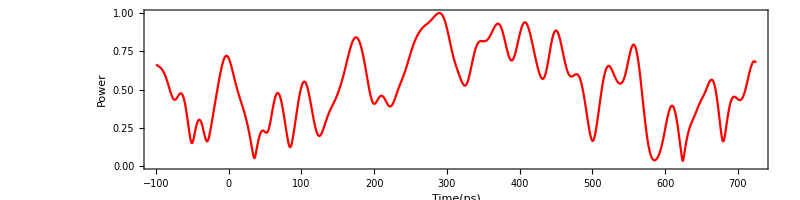

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

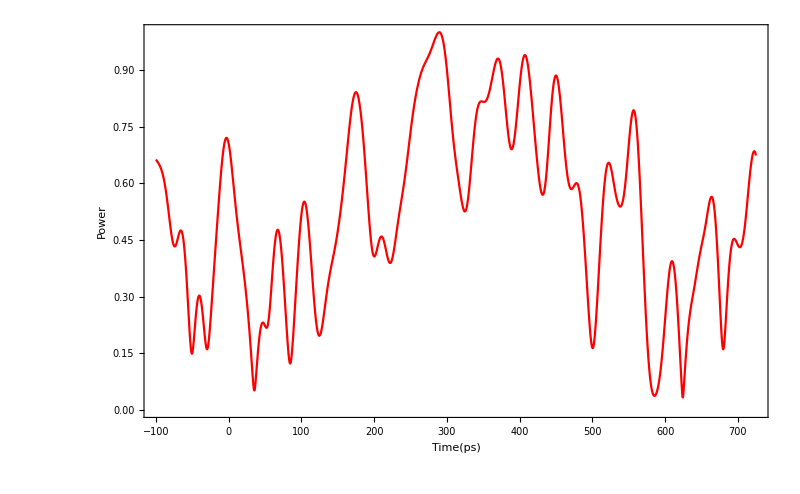

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->40,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

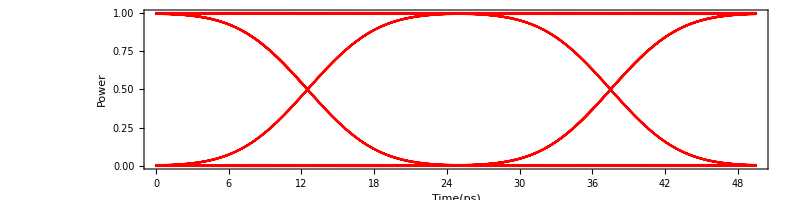

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

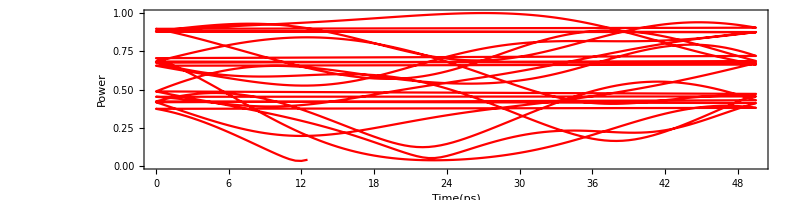

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 81 point

0 is 51 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.680821

Average of 0 is 0.202646

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.144097

A Standard Deviation of 0 is 0.147935

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

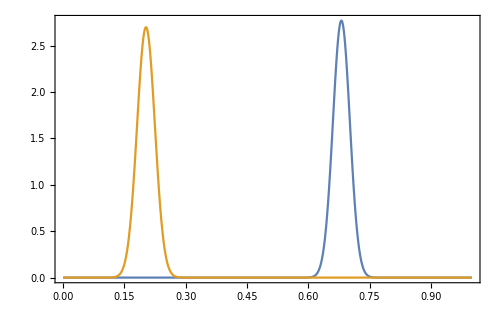

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 1.6374

Q-dB is 4.28311 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.0507731

Eye Opening is 0.389277

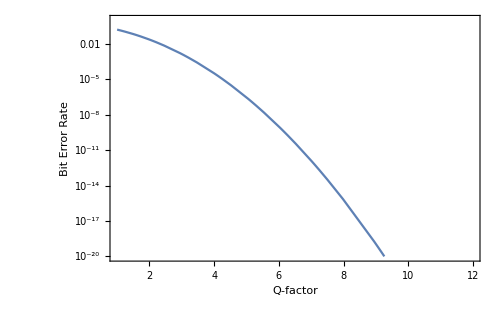

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```